### Initialize

#### Data and path length function

```mathematica
method="Driving";(*"Driving","Biking","Walking"*)
quantity="TravelDistance";(*"TravelDistance","TravelTime"*)
```

```mathematica
n=70;(*number of cities, n=3,4,5,7,10,15*)
r=Take[CityData[{All,"Ukraine"}],n](*take n largest cities*)
x0=RandomSample[Range[n]](*initial path*)
```

{Kyiv,Kharkiv,Odesa,Dnipro,Donetsk,Zaporizhzhya,Lviv,Kryvyy Rih,Mykolayiv,Mariupol,Luhansk,Sevastopol,Vinnytsya,Makiyivka,Kherson,Simferopol,Poltava,Chernihiv,Cherkasy,Sumy,Zhytomyr,Chernivtsi,Rivne,Horlivka,Khmelnytskyi,Dniprodzerzhynsk,Kirovohrad,Ivano-Frankivsk,Kremenchuk,Ternopil,Lutsk,Bila Tserkva,Kramatorsk,Melitopol,Kerch,Nikopol,Slavyansk,Berdyansk,Uzhhorod,Syeverodonetsk,Alchevsk,Yevpatoriya,Pavlohrad,Sverdlovsk,Lysychansk,Kamyanets-Podilskyy,Konotop,Krasnyy Luch,Brovary,Uman,Mukacheve,Stakhanov,Shostka,Yenakiyive,Alexandria,Yalta,Drohobych,Berdychiv,Bakhmut,Kostyantynivka,Izmayil,Nizhyn,Novomoskovsk,Kovel,Smila,Pervomaysk,Feodosiya,Kalush,Chervonohrad,Torez}

{49,64,65,16,69,28,29,20,4,13,10,60,21,2,53,46,37,36,35,63,6,55,27,54,12,67,7,17,39,31,5,38,57,14,58,15,34,25,48,9,42,30,47,33,62,50,52,43,70,1,26,24,22,23,59,3,19,11,45,18,32,8,51,44,66,56,68,61,40,41}

```mathematica
TD[path_]:=TravelDirections[path,TravelMethod->method]
```

```mathematica
AbsoluteTiming[
unit=Switch[quantity,"TravelDistance",Quantity[1, "Kilometers"],"TravelTime",Quantity[1, "Minutes"]];
L=ParallelTable[0,{n},{n}];(*distance matrix, dimensionless - faster computations*)
For[i=1,i≤n,i++,
L⟦i,i⟧=0;
For[j=i+1,j≤n,j++,
L⟦i,j⟧=TD[{r⟦i⟧,r⟦j⟧}][quantity]/unit;(*travel distance between cities r⟦i⟧ and r⟦j⟧ in kilometers*)
L⟦j,i⟧=L⟦i,j⟧;
]
]
]
(*L//MatrixForm*)
```

{1335.93,Null}

```mathematica
f[x_]:=Sum[L⟦x⟦i⟧,x⟦i+1⟧⟧,{i,1,n-1}];(*path length*)
```

```mathematica
f[x0]
```

43976.1

#### Visualization

```mathematica
path[x_, iter_]:=Legended[GeoGraphics[{Red,Thick,TD[r[[x]]]["TravelPath"],Table[GeoMarker[r[[i]],Graphics[Disk[]],"Color"->Black,"Scale"->0.07],{i,1,n}]},GeoRange->Entity["Country","Ukraine"],ImageSize->1000],Placed[Text[Style["iter = "<>ToString[iter]<>"  "<>Switch[quantity,"TravelDistance","f(x) = "<>ToString[Round[f[x]]]<>" km","TravelTime","f(x) = "<>ToString[UnitConvert[Quantity[Round[f[x]],"min"],MixedUnit[{"h","min"}]]]],Large]],Below]]
```

```mathematica
path[x0, 0]
```

### Generators of a random neighbour

#### 1) Exchange of two neighbouring points

```mathematica
neighbourA[x_]:=Module[{xn=x,i},i=RandomInteger[{1,Length[x]-1}];
{xn[[i]],xn[[i+1]]}={xn[[i+1]],xn[[i]]};
xn];
```

#### 2) Exchange of two random points

```mathematica
neighbourB[x_]:=Module[{xn=x,i,j},{i,j}=RandomSample[Range[Length[x]],2];
{xn[[i]],xn[[j]]}={xn[[j]],xn[[i]]};
xn];
```

#### 3) Reverse sequence between two random points

```mathematica
neighbourC[x_]:=Module[{xn=x,i,j},{i,j}=Sort[RandomSample[Range[Length[x]],2]];
xn[[i;;j]]=Reverse[xn[[i;;j]]];
xn];
```

### Probability function

```mathematica
P[df_,T_]:=Min[1,Exp[-df/T]];
Manipulate[Plot[P[df,T],{df,-200,500},PlotRange->{0,1.05},AxesLabel->{"df [km]","P"},PlotLabel->Row[{"T = ",T}]],{{T,50},1,500}]
```

### Find T0 empirically

Set T0 so that approximately 1/2 of longer paths are accepted

```mathematica
(*random walk:zbiera kladne df hodnoty,riesi Exp[-<df+>/T0]=0.5*)
findT0[x0_,neighbour_,samples_:1000]:=Module[{x=x0,xnew,df,dfList={}},Do[xnew=neighbour[x];
df=f[xnew]-f[x];
If[df>0,AppendTo[dfList,df]];
x=xnew,{samples}];
-Mean[dfList]/Log[0.5]];

T0auto=findT0[x0,neighbourC];
Print["T0 = ",T0auto," km"]
```

T0 = 579.822 km

### Algorithm

```mathematica
X={x0};

alpha=0.99;   
Tmin=0.00001;  
kmax=50;     
T=T0auto;

While[T>Tmin,Do[xnew=neighbourC[Last[X]];
df=f[xnew]-f[Last[X]];
If[P[df,T]>=RandomReal[],AppendTo[X,xnew]],{kmax}];
T=alpha*T;];

Print["Steps stored : ",Length[X]];
Print["Initial f    : ",f[x0]," km"];
Print["Final   f    : ",f[Last[X]]," km"]
```

General::munfl: Exp[-715.739] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-814.045] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.738] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Steps stored : 3848

Initial f    : 43976.1 km

Final   f    : 6910.45 km

```mathematica
orderCrossover[p1_,p2_]:=Module[{m=Length[p1],i,j,seg,rest},{i,j}=Sort[RandomSample[Range[m],2]];
seg=p1[[i;;j]];
rest=Select[p2,!MemberQ[seg,#]&];
Join[rest[[1;;i-1]],seg,rest[[i;;]]]];
tournamentSelect[population_,fvals_,tournSize_:3]:=Module[{idx},idx=RandomSample[Range[Length[population]],tournSize];
population[[idx[[First[Ordering[fvals[[idx]],1]]]]]]];
geneticAlgorithm[popSize_,nElite_,ngen_,Pm_,neighbour_,tournSize_:4]:=Module[{pop,fvals,eliteIdx,newPop,p1,p2,child,bestIdx,history},
pop=Table[RandomSample[Range[n]],{popSize}];
fvals=f/@pop;
bestIdx=First[Ordering[fvals,1]];
history={{pop[[bestIdx]],1,fvals[[bestIdx]]}};
Do[
(*elitism*)
eliteIdx=Ordering[fvals,nElite];
newPop=pop[[eliteIdx]];
(*crossover+mutation*)
While[Length[newPop]<popSize,
p1=tournamentSelect[pop,fvals,tournSize];
p2=tournamentSelect[pop,fvals,tournSize];
child=orderCrossover[p1,p2];
If[RandomReal[]<=Pm,child=neighbour[child]];
AppendTo[newPop,child];];
pop=newPop;
fvals=f/@pop;
bestIdx=First[Ordering[fvals,1]];
AppendTo[history,{pop[[bestIdx]],gen,fvals[[bestIdx]]}],{gen,2,ngen}];
history];
```

```mathematica
popSize=200;
nElite=60;
ngen = 600;
Pm=0.5;
tournSz=3;

historyGA=geneticAlgorithm[popSize,nElite,ngen,Pm,neighbourC,tournSz];

Print["Generations : ",Length[historyGA]];
Print["Initial f   : ",historyGA[[1,3]]];
Print["Final   f   : ",historyGA[[-1,3]]];
```

Generations : 600

Initial f   : 36896.3

Final   f   : 6787.18

### Visualization

```mathematica
(*Manipulate[path[X⟦k⟧],{k,1,Length[X],1}]*)
```

```mathematica
(*best solution*)
{{xBest=Last[X];}, {□}}
Print["Best route : ",EntityValue[r[[xBest]],"Name"]]

Print["Length     : ",f[xBest]," km"];
path[xBest, Length[X]]
```

{{Null},{□}}

Best route : {Izmayil,Odesa,Mykolayiv,Kherson,Pervomaysk,Uman,Vinnytsya,Khmelnytskyi,Ternopil,Kamyanets-Podilskyy,Chernivtsi,Ivano-Frankivsk,Kalush,Mukacheve,Uzhhorod,Drohobych,Lviv,Chervonohrad,Kovel,Lutsk,Rivne,Zhytomyr,Berdychiv,Bila Tserkva,Kyiv,Brovary,Chernihiv,Nizhyn,Konotop,Shostka,Sumy,Cherkasy,Smila,Kirovohrad,Kryvyy Rih,Alexandria,Kremenchuk,Poltava,Kharkiv,Slavyansk,Kramatorsk,Kostyantynivka,Bakhmut,Lysychansk,Syeverodonetsk,Stakhanov,Alchevsk,Luhansk,Sverdlovsk,Krasnyy Luch,Torez,Yenakiyive,Horlivka,Makiyivka,Donetsk,Pavlohrad,Novomoskovsk,Dnipro,Dniprodzerzhynsk,Nikopol,Zaporizhzhya,Mariupol,Berdyansk,Melitopol,Simferopol,Yevpatoriya,Sevastopol,Yalta,Feodosiya,Kerch}

Length     : 6910.45 km

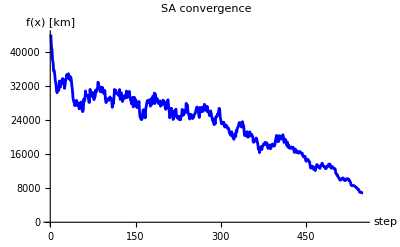

```mathematica
ListLinePlot[f/@X[[1;;-1;;Max[1,Floor[Length[X]/500]]]],PlotLabel->"SA convergence",AxesLabel->{"step","f(x) [km]"},PlotStyle->Blue]
```

```mathematica
{{xBestGA=historyGA[[-1, 1]];}, {□}}
Print["Best route : ",EntityValue[r[[xBestGA]],"Name"]]

Print["Length     : ",f[xBestGA]," km"];
path[xBestGA, Length[xBestGA]]
```

{{Null},{□}}

Best route : {Kerch,Feodosiya,Yalta,Sevastopol,Simferopol,Yevpatoriya,Kherson,Mykolayiv,Odesa,Izmayil,Pervomaysk,Uman,Bila Tserkva,Smila,Cherkasy,Kremenchuk,Alexandria,Kirovohrad,Kryvyy Rih,Nikopol,Zaporizhzhya,Melitopol,Berdyansk,Mariupol,Donetsk,Makiyivka,Horlivka,Yenakiyive,Torez,Krasnyy Luch,Sverdlovsk,Luhansk,Alchevsk,Stakhanov,Syeverodonetsk,Lysychansk,Bakhmut,Slavyansk,Kramatorsk,Kostyantynivka,Pavlohrad,Novomoskovsk,Dnipro,Dniprodzerzhynsk,Poltava,Kharkiv,Sumy,Shostka,Konotop,Nizhyn,Chernihiv,Brovary,Kyiv,Zhytomyr,Berdychiv,Vinnytsya,Khmelnytskyi,Kamyanets-Podilskyy,Chernivtsi,Ternopil,Rivne,Lutsk,Kovel,Chervonohrad,Lviv,Ivano-Frankivsk,Kalush,Drohobych,Mukacheve,Uzhhorod}

Length     : 6787.18 km

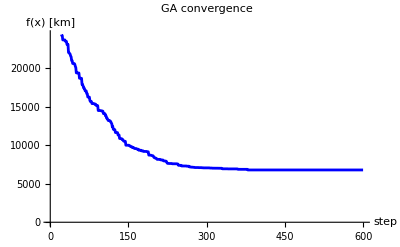

```mathematica
ListLinePlot[f/@historyGA[[1;;-1;;Max[1,Floor[Length[historyGA]/1000]], 1]],PlotLabel->"GA convergence",AxesLabel->{"step","f(x) [km]"},PlotStyle->Blue]
```

```mathematica
saIdx=Range[1,Length[X],Max[1,Floor[Length[X]/100]]];
gaIdx=Range[1,Length[historyGA],Max[1,Floor[Length[historyGA]/100]]];

saFrames=X[[saIdx]];
gaFrames=historyGA[[gaIdx]];
Length[saFrames]
Length[gaFrames]
```

102

100

```mathematica
saImages=Table[path[saFrames[[k]],saIdx[[k]]],{k,Length[saFrames]}];
```

```mathematica
gaImages=Table[path[gaFrames[[k, 1]],gaIdx[[k]]],{k,Length[gaFrames]}];
```

```mathematica
saDir="SA_frames";
gaDir="GA_frames";

CreateDirectory[saDir];
CreateDirectory[gaDir];
```

```mathematica
ParallelDo[Export[FileNameJoin[{saDir,StringPadLeft[ToString[i],5,"0"]<>".png"}],saImages[[i]]],{i,Length[saImages]}];
```

```mathematica
ParallelDo[Export[FileNameJoin[{gaDir,StringPadLeft[ToString[i],5,"0"]<>".png"}],gaImages[[i]]],{i,Length[gaImages]}];
```